```mathematica
f2[x_, y_]:=x^3+4+y^2
```

```mathematica
Plot3D[f2[x,y],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

```mathematica
MinValue[f2[x,y],{x,y}]
```

-∞

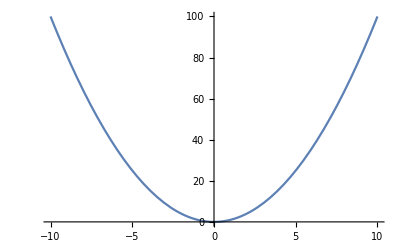

```mathematica
f[x_]:=x^2
Plot[f[x],{x,-10,10}]
```

```mathematica
FrankWolfe[f_,a_,b_,eps_] := (
k=0;
Subscript[x, k]= RandomReal[{a,b}];
Subscript[x, k+1]=Subscript[x, k]+1;
Print[Subscript[x, k],Subscript[x, k+1]];
While[Abs[f'[Subscript[x, k]]-f'[Subscript[x, k+1]]]>eps && k<1000,(
k++;
(* Step 1: Direction-finding subproblem *)
Subscript[s, k]/.Minimize[{s*f'[Subscript[x, k]], a≤s≤b},{s}][[2]];
Print[Subscript[s, k]];
(* Step 2: Step size determination *)
gamma=2/(k+2);
(* Step 3: Update *)
Subscript[x, k]=Subscript[x, k+1];
Subscript[x, k+1]=Subscript[x, k]+gamma*(Subscript[s, k]-Subscript[x, k]);
)];
)
```

```mathematica
f'[x]==0
```

2 x==0

```mathematica
Minimize[{s*f'[3],-10≤s≤10},{s}][[2]]
```

{s→-10}

```mathematica
FrankWolfe[f, -10, 10, 10^(-4)]
```

-9.03571-8.03571

{s→10.}

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 2/3\ ((s → 10.) - x_2) + x_2.